```mathematica
rhor=1;rhos=1.49167;
Cpr=1;Cps=0.567331;
kappar=0.885347;kappas=38.5126;
n=1.2;
A=120.9;(*120.9;*)
R=8.31;
Ea=8*R;
(*Ea=15.5583*R;*)
Htr=0.942895; (*1.06189;*)(*0.942895*)
T0=1;Ts=400./300.;
tmax=20;xmax=10;
```

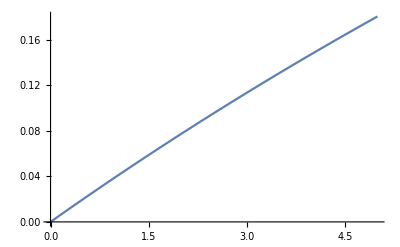

```mathematica
NDSolve[{y'[t]==((1-y[t])^n)*A*Exp[-Ea/(R*T0)], y[0]==0.},y,{t,0,tmax}];
Plot[y[t]/.%,{t,0,tmax},PlotRange->Full]
```

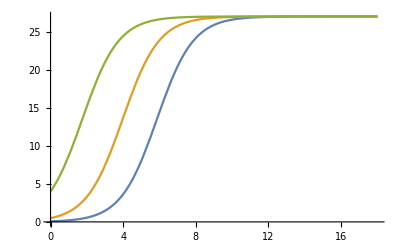

```mathematica
DSolve[{y'[x]==y[x] (1-y[x]/27),y[0]==a},y,x]//Quiet;
Plot[Evaluate[y[x]/.%/.{{a->1/13},{a->1/2},{a->4}}],{x,0,18}]
```

Uniform distribution of Temperature

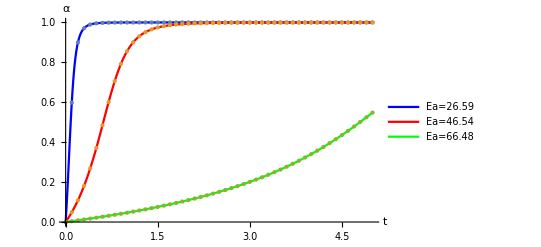

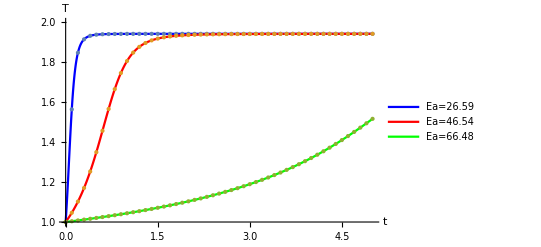

```mathematica
sol=ParametricNDSolve[{rhor*Cpr*T'[t]== Htr*rhor*y'[t], y'[t]==((1-y[t])^n)*A*Exp[-Eaa/(R*T[t])], y[0]==0., T[0]== 1},{y,T},{t,0,tmax},{Eaa}];
yy=Table [{t,y[Eaa][t]/.sol}, {Eaa, 0.4*Ea,1.*Ea, 0.3*Ea}, {t, 0, tmax, 0.02*tmax}];
yytheory=Table [{t,y[Eaa][t]/.sol}, {Eaa, 0.4*Ea,1.*Ea, 0.3*Ea}, {t, 0, tmax, 0.001*tmax}];
TT=Table [{t,T[Eaa][t]/.sol}, {Eaa, 0.4*Ea,1.*Ea, 0.3*Ea},{t, 0, tmax, 0.02*tmax}];
TTtheory=Table [{t,T[Eaa][t]/.sol}, {Eaa, 0.4*Ea,1.*Ea, 0.3*Ea},{t, 0, tmax, 0.001*tmax}];
Show[ListLinePlot[{yytheory[[1]], yytheory[[2]], yytheory[[3]]},
PlotRange->{{0,tmax},{0,1}},
PlotStyle->{{Blue}, Red, Green},
LabelStyle->Directive[Black,12,FontFamily->"Times"], 
AxesOrigin->{0,0},
AxesLabel->{
Style["t",Black,FontFamily->"Times",FontSize->20],
Style["α",Black,FontFamily->"Times",FontSize->20]},
PlotLegends->{"Ea="<>ToString[NumberForm[0.4*Ea,4]],"Ea="<>ToString[NumberForm[0.7*Ea,4]],"Ea="<>ToString[NumberForm[Ea,4]]}],
ListPlot[{yy[[1]], yy[[2]], yy[[3]]},PlotStyle->PointSize[Medium], PlotStyle->{{LightBlue}, LightRed, LightGreen}]]
Show[ListLinePlot[{TTtheory[[1]], TTtheory[[2]], TTtheory[[3]]},
PlotRange->{{0,tmax},{1,2}},
PlotStyle->{{Blue}, Red, Green},
LabelStyle->Directive[Black,12,FontFamily->"Times"], 
AxesOrigin->{0,1},
AxesLabel->{
Style["t",Black,FontFamily->"Times",FontSize->20],
Style["T",Black,FontFamily->"Times",FontSize->20]},
PlotLegends->{"Ea="<>ToString[NumberForm[0.4*Ea,4]],"Ea="<>ToString[NumberForm[0.7*Ea,4]],"Ea="<>ToString[NumberForm[Ea,4]]}],
ListPlot[{TT[[1]], TT[[2]], TT[[3]]},PlotStyle->PointSize[Medium], PlotStyle->{{LightBlue}, LightRed, LightGreen}]]
```

Polymerization on Heated Wall

0.1

-Graphics3D-

-Graphics3D-

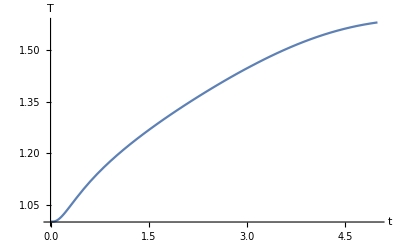

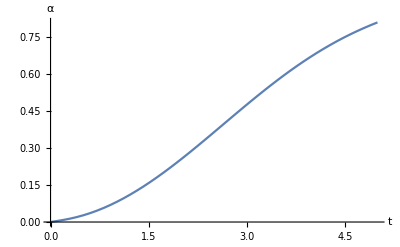

```mathematica
xslice=0.1
sol=ParametricNDSolve[{rhor*Cpr*D[T[t,x],t]== kappar*D[T[t,x],x,x]+Htr*rhor*D[y[t,x],t], D[y[t,x],t]==((1-y[t,x])^n)*A*Exp[-Eaa/(R*T[t,x])], y[0,x]==0., T[0,x]== 1,T[t,0]==T0+(Ts-T0)*Tanh[100*t],(D[T[t,x],x]/.x->xmax)==0},{y,T},{t,0,tmax},{x,0,xmax},{Eaa}];
Plot3D[Evaluate[T[Ea][t,x]/.sol],{t,0,tmax},{x,0,xmax}, PlotRange->All, AxesLabel->{"t", "x","T"}]
Plot3D[Evaluate[y[Ea][t,x]/.sol],{t,0,tmax},{x,0,xmax}, PlotRange->All, AxesLabel->{"t", "x", "α"}]
Plot[Evaluate[T[Ea][t,rslice]/.sol],{t,0,tmax}, PlotRange->All, AxesLabel->{"t", "T"}]
Plot[Evaluate[y[Ea][t,rslice]/.sol],{t,0,tmax}, PlotRange->All, AxesLabel->{"t", "α"}]
```

```mathematica
tfix=0.234797;
Print["T=", T[Ea][tfix,xslice]/.sol,", α=", y[Ea][tfix,xslice]/.sol]
```

T=1.38866, α=0.490255

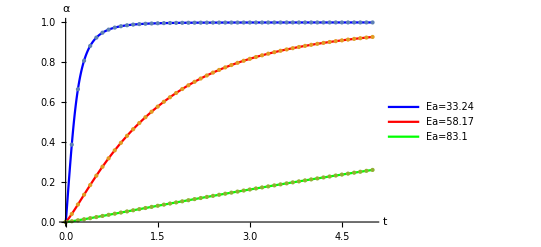

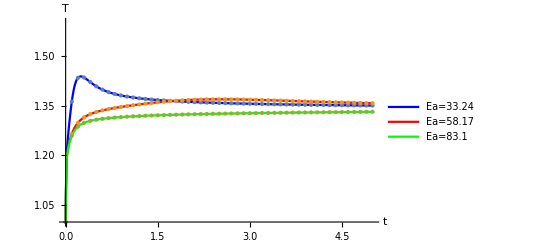

```mathematica
yy=Table [{t,y[Eaa][t, xslice]/.sol}, {Eaa, 0.4*Ea,1.*Ea, 0.3*Ea}, {t, 0, tmax, 0.02*tmax}];
yytheory=Table [{t,y[Eaa][t, xslice]/.sol}, {Eaa, 0.4*Ea,1.*Ea, 0.3*Ea}, {t, 0, tmax, 0.001*tmax}];
TT=Table [{t,T[Eaa][t, xslice]/.sol}, {Eaa, 0.4*Ea,1.*Ea, 0.3*Ea},{t, 0, tmax, 0.02*tmax}];
TTtheory=Table [{t,T[Eaa][t, xslice]/.sol}, {Eaa, 0.4*Ea,1.*Ea, 0.3*Ea},{t, 0, tmax, 0.001*tmax}];
Show[ListLinePlot[{yytheory[[1]], yytheory[[2]], yytheory[[3]]},
PlotRange->{{0,tmax},{0,1}},
PlotStyle->{{Blue}, Red, Green},
LabelStyle->Directive[Black,12,FontFamily->"Times"], 
AxesOrigin->{0,0},
AxesLabel->{
Style["t",Black,FontFamily->"Times",FontSize->20],
Style["α",Black,FontFamily->"Times",FontSize->20]},
PlotLegends->{"Ea="<>ToString[NumberForm[0.4*Ea,4]],"Ea="<>ToString[NumberForm[0.7*Ea,4]],"Ea="<>ToString[NumberForm[Ea,4]]}],
ListPlot[{yy[[1]], yy[[2]], yy[[3]]},PlotStyle->PointSize[Medium], PlotStyle->{{LightBlue}, LightRed, LightGreen}]]
Show[ListLinePlot[{TTtheory[[1]], TTtheory[[2]], TTtheory[[3]]},
PlotRange->{{0,tmax},{1,1.6}},
PlotStyle->{{Blue}, Red, Green}, 
LabelStyle->Directive[Black,12,FontFamily->"Times"], 
AxesOrigin->{0,1},
AxesLabel->{
Style["t",Black,FontFamily->"Times",FontSize->20],
Style["T",Black,FontFamily->"Times",FontSize->20]},
PlotLegends->{"Ea="<>ToString[NumberForm[0.4*Ea,4]],"Ea="<>ToString[NumberForm[0.7*Ea,4]],"Ea="<>ToString[NumberForm[Ea,4]]}],
ListPlot[{TT[[1]], TT[[2]], TT[[3]]},PlotStyle->PointSize[Medium], PlotStyle->{{LightBlue}, LightRed, LightGreen}]]
```

```mathematica
Polymerization around Heated Cylinder
```

-Graphics3D-

-Graphics3D-

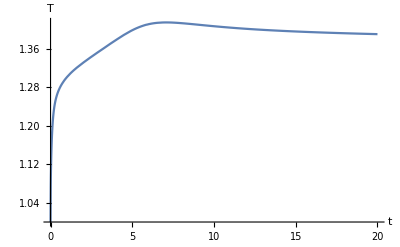

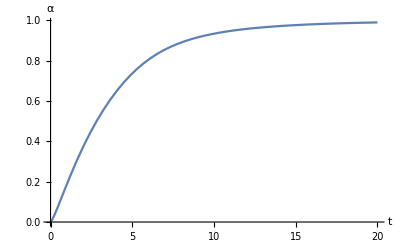

```mathematica
rslice=1.2;
rmin=1;
rmax=10;
sol=ParametricNDSolve[{rhor*Cpr*D[T[t,r],t]== kappar*(D[T[t,r],r,r]+D[T[t,r],r]/r)+Htr*rhor*D[y[t,r],t], D[y[t,r],t]==((1-y[t,r])^n)*A*Exp[-Eaa/(R*T[t,r])], y[0,r]==0., T[0,r]== 1,T[t,rmin]==T0+(Ts-T0)*Tanh[100*t],(D[T[t,r],r]/.r->rmax)==0},{y,T},{t,0,tmax},{r,rmin,rmax},{Eaa}];
Plot3D[Evaluate[T[Ea][t,r]/.sol],{t,0,tmax},{r,rmin,rmax}, PlotRange->All, AxesLabel->{"t", "r","T"}]
Plot3D[Evaluate[y[Ea][t,r]/.sol],{t,0,tmax},{r,rmin,rmax}, PlotRange->All, AxesLabel->{"t", "r", "α"}]
Plot[Evaluate[T[Ea][t,rslice]/.sol],{t,0,tmax}, PlotRange->All, AxesLabel->{"t", "T"}]
Plot[Evaluate[y[Ea][t,rslice]/.sol],{t,0,tmax}, PlotRange->All, AxesLabel->{"t", "α"}]
```

```mathematica
Manipulate[Show[RevolutionPlot3D[{Evaluate[T[Ea][tf,r]/.sol]},{r,rmin,rmax}],Plot3D[0,{x,-rmax,rmax},{y,-rmax,rmax}, PlotStyle->Gray], PlotRange->All],{tf, 0.1, tmax}]
```

```mathematica
Manipulate[Show[RevolutionPlot3D[{Evaluate[y[Ea][tf,r]/.sol]},{r,rmin,rmax}],Plot3D[0,{x,-rmax,rmax},{y,-rmax,rmax}, PlotStyle->Gray], PlotRange->All],{tf, 0.1, tmax}]
```

```mathematica
tfix=19.43;
rfix=1.2;
Print["T=", T[Ea][tfix,rfix]/.sol,", α=", y[Ea][tfix,rfix]/.sol]
```

T=1.39046, α=0.988809

```mathematica
dataset = Table[{tf,T[Ea][tf,rslice]/.sol, y[Ea][tf,rslice]/.sol}, {tf, 0., tmax,0.01}];
Export["/home/e.sharaborin/basilisk/work/Heat_transfer_Polymerization/Verif/cylinder_polymerization_wolfram_r="<>ToString[rslice]<>".csv",dataset,"CSV", "TableHeadings"->{"t", "T", "alpha"}]
```

/home/e.sharaborin/basilisk/work/Heat_transfer_Polymerization/Verif/cylinder_polymerization_wolfram_r=1.2.csv